```mathematica
Quit[];
```

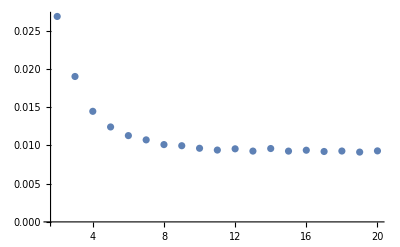

```mathematica
Dat=Import[FileNameJoin[{NotebookDirectory[], "RMPS", "build", "Debug", "output_for N.txt"}], "csv"] // Drop[#, 3] &;
ListPlot[({#[[1]],#[[3]]/(#[[2]])^2}&)/@Dat,PlotRange->All]
```

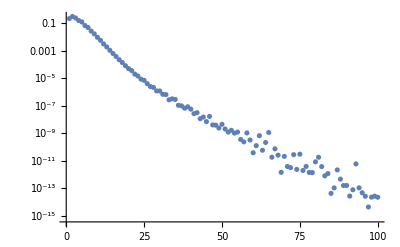

```mathematica
Dat=Import[FileNameJoin[{NotebookDirectory[], "RMPS", "build", "Debug", "output_for Ns.txt"}], "csv"] // Drop[#, 2] &;
ListLogPlot[({#[[1]],#[[3]]/(#[[2]])^2}&)/@Dat]
```

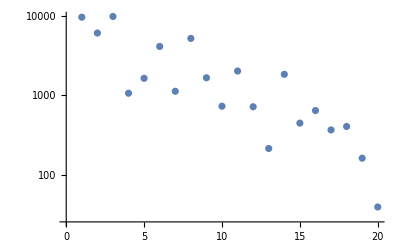

```mathematica
Dat=Import[FileNameJoin[{NotebookDirectory[], "RMPS", "build", "Debug", "output_for N 2.txt"}], "csv"] // Drop[#, 2] &;
ListLogPlot[({#[[1]],#[[3]]/(#[[2]])^2}&)/@Dat]
```

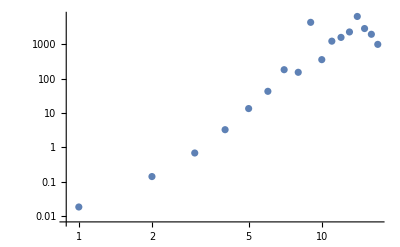

```mathematica
Dat=Import[FileNameJoin[{NotebookDirectory[], "RMPS", "build", "Debug", "output_for Ns 2.txt"}], "csv"] // Drop[#, 2] &;
ListLogLogPlot[({#[[1]],#[[3]]/(#[[2]])^2}&)/@Dat]
```

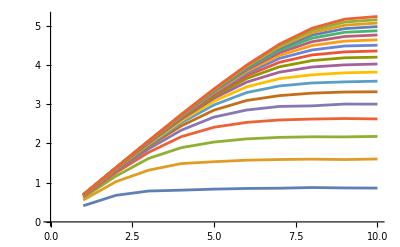

```mathematica
Dat=Import[FileNameJoin[{NotebookDirectory[], "RMPS", "build", "Debug", "output_entropy.txt"}], "csv"] // Drop[#, 3] &;
ListPlot[Partition[({#[[2]],#[[3]]}&)/@Dat,10],Joined->True]
```